```mathematica
Quit[];
```

```mathematica
openVideo[fname_,w_,h_]:=Module[{},
video["stream"]=OpenRead["!/usr/local/bin/ffmpeg -i  "~~fname~~" -loglevel quiet -f image2pipe -pix_fmt gray -vcodec rawvideo -",BinaryFormat->True];
video["SkipFrame",n_Integer: 1]:=Skip[video["stream"],Byte,n*1*w*h];
video["NextFrame"]:=Partition[Partition[BinaryReadList[video["stream"],"Byte",1*w*h],1],w];
video["NextFrame",n_Integer]:=Table[video["NextFrame"],{n}];
video["NextImage"]:=Image[video["NextFrame"],"Byte"];
video["NextImage",n_Integer]:=Table[video["NextImage"],{n}];
video["stream"]]
```

#### Test basic methods

```mathematica
Quit[];
```

```mathematica
AppendTo[$Path, "C:\\Users\\km558\\Dropbox\\PhD\\Software\\video-tracking\\bin\\packages\\"];
<<VideoTracking`
```

```mathematica
FFmpeg[]
```

ffmpeg does not respond correctly. Please check the path: ffmpeg.exe

```mathematica
FFImport["D:\\25\\1\\video_0.avi", {"Frames",55000}]//AbsoluteTiming
```

{69.52195,-Graphics-}

```mathematica
FFImport["D:\\25\\1\\video_0.avi", {"Frames", {55000}, True}]//AbsoluteTiming
```

experimental frame grabber - ffmpeg

{79.49895,{-Graphics-}}

```mathematica
Import["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/test_video.avi", {"Frames",1}]//AbsoluteTiming
```

{0.06733,-Graphics-}

#### Test if there is such thing

```mathematica
path = "/usr/local/bin/ffmpeg";

StringMatchQ[ ToString@ReadLine[OpenRead["!"~~path~~" -version", BinaryFormat->True]] , "ffmpeg version 2.*"]
```

True

#### Testing input for the functions

```mathematica
elements = {"Frames", 1};

Switch[ elements, 
{"Frames",_Integer}, "one number",
{"Frames",{_Integer,_}}, "vector",
{_String, _}, "Command",
_, "not"
]
```

one number

```mathematica
Import["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/test_video.avi", "FrameRate"]
```

30.

#### Test if frame seeker gets the right frame

```mathematica
Quit[]
```

```mathematica
vid = "D:\\25\\1\\video_0.avi";
```

```mathematica
CompateImports[frame_,offset_:0]:=Module[{img0,img1 },
img0 =FFImport[vid, {"Frames",{frame+offset}}][[1]];
img1 = FFImport[vid, {"Frames",{frame}, True}][[1]];
ImageDifference[img0,img1]
]
```

```mathematica
cc = Table[ Total[ImageData@CompateImports[300, i], 3] , {i,Range[-5,5]}]
```

{78329.6,78510.3,78395.,78228.4,78089.7,77615.4,78229.6,78347.3,78531.1,78758.4,78843.9}

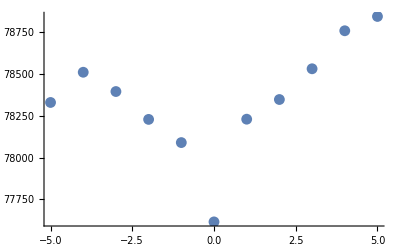

```mathematica
ListPlot[ Transpose@ { Range[-5,5], cc} ]
```

```mathematica
CompateImports[57851, 0]//ImageAdjust
```

-Graphics-

#### Test take multiple frames

```mathematica
setImg0 = FFImport[vid, {"Frames",{1,2,10,21,1000,10000}}];
```

```mathematica
setImg1 = Import[vid, {"Frames",{1,2,10,21,1000,10000}}];

ImageDifference[#⟦1⟧, #⟦2⟧]&/@(Transpose@ {setImg0, setImg1})
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
setImg0 = FFImport[vid, {"Frames", Range[1000, 3000]}];
setImg1 = Import[vid, {"Frames",Range[1000, 3000]}];

ImageDifference[#⟦1⟧, #⟦2⟧]&/@(Transpose@ {setImg0, setImg1})
```

#### Speed test

```mathematica
Quit[]
```

```mathematica
no = 5;
start = 40000;

vid = "D:\\25\\1\\video_0.avi";

"ffmpeg"-> AbsoluteTiming[FFImport[vid, {"Frames",Range[start,no+start]}]]⟦1⟧

"ffmpeg new"-> AbsoluteTiming[FFImport[vid, {"Frames",Range[start,no+start], True}]]⟦1⟧

"QuickTime"-> AbsoluteTiming[Import[vid, {"Frames",Range[start,no+start]}]]⟦1⟧
```

ffmpeg→50.45705

experimental frame grabber - ffmpeg

ffmpeg new→440.09701

QuickTime→0.83108

#### Compare method with fast skip and without

```mathematica
setImg0 = FFImport["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/test_video.avi", {"Frames",Range[904,910], True}];

setImg1 = FFImport["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/test_video.avi", {"Frames",Range[904,910]}];

ImageDifference[#⟦1⟧, #⟦2⟧]&/@(Transpose@ {setImg0, setImg1})
```

InputStream[…]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Streams[]
```

{OutputStream[…],OutputStream[…]}